# Energía de ligadura I

## Constantes

```mathematica
me=0.51099895069; (*MeV/c^2*)
mn=939.56542194; (*MeV/c^2*)
mp=938.27208943; (*MeV/c^2*)
uma=931.49410372; (*MeV/c^2*)
```

## Carga de datos

```mathematica
data = Import["C:\\Users\\ruben\\Desktop\\Prácticas Nuclear\\Práctica 1 Radio nuclear y energía de ligadura nuclear. Ficheros-20260304\\excesodemasas.txt", "Table"];
data2=Rest[data];
```

```mathematica
datosAZM = Select[
   data2,
   Length[#] >= 7 && NumericQ[#[[1]]] && NumericQ[#[[3]]] && NumericQ[#[[7]]] &
][[All, {1, 3, 7}]];
```

## Binding Energy

```mathematica
B[A_, Z_, M_] := Z*mp + (A - Z)*mn + Z*me - (M + A*uma);
BA[A_, Z_, M_] := B[A, Z, M]/A;
```

## Representación 3D

```mathematica
(*resultadoB = ({#[[1]], #[[2]], -B[#[[1]], #[[2]], #[[3]]]} &) /@ datosAZM;
ListPointPlot3D[
  resultadoB,
  AxesLabel -> {"A", "Z", "B (MeV)"},
  PlotStyle -> PointSize[0.008],
  ColorFunction -> "TemperatureMap",
  ColorFunctionScaling -> True,
  PlotLegends -> BarLegend[{"TemperatureMap", Automatic}],
  ImageSize -> Large
]*)
resultadoBA = ({#[[2]], #[[1]], -BA[#[[1]], #[[2]], #[[3]]]} &) /@ datosAZM;
ListPointPlot3D[
  resultadoBA,
  AxesLabel -> {"Z", "A", "-B/A (MeV)"},
  PlotStyle -> PointSize[0.01],
  ColorFunction -> (ColorData["Rainbow"][Rescale[#3, {-9, -7}]] &),
  ColorFunctionScaling -> False,
  BoxRatios -> {1, 1, 0.6},
  ViewPoint -> {2.2, -2.4, 1.4},
  ViewVertical -> {0, 0, 1},
  SphericalRegion -> True,
  PlotLegends -> BarLegend["Rainbow"],
  ImageSize -> Large
]
datosFiltrados = Select[resultadoBA, 75 <= #[[2]] <= 200 &];
ListPointPlot3D[
  datosFiltrados,
  AxesLabel -> {"Z", "A", "-B/A (MeV)"},
  PlotStyle -> PointSize[0.01],
  ColorFunction -> (ColorData["Rainbow"][Rescale[#3, {-9, -7}]] &),
  ColorFunctionScaling -> False,
  BoxRatios -> {1, 1, 0.6},
  ViewPoint -> {2.2, -2.4, 1.4},
  ViewVertical -> {0, 0, 1},
  SphericalRegion -> True,
  PlotLegends -> BarLegend["Rainbow"],
  ImageSize -> Large
]
```

-Graphics3D-

-Graphics3D-

# Parábola de masa

## Carga de datos

Datos usados:

Z | Exceso de masa | Elemento
23 | -46.08 | V
24 | -55.2812 | Cr
25 | -56.9108 | Mn
26 | -60.6063 | Fe
27 | -56.0397 | Co
28 | -53.9068 | Ni
29 | -38.2 | Cu

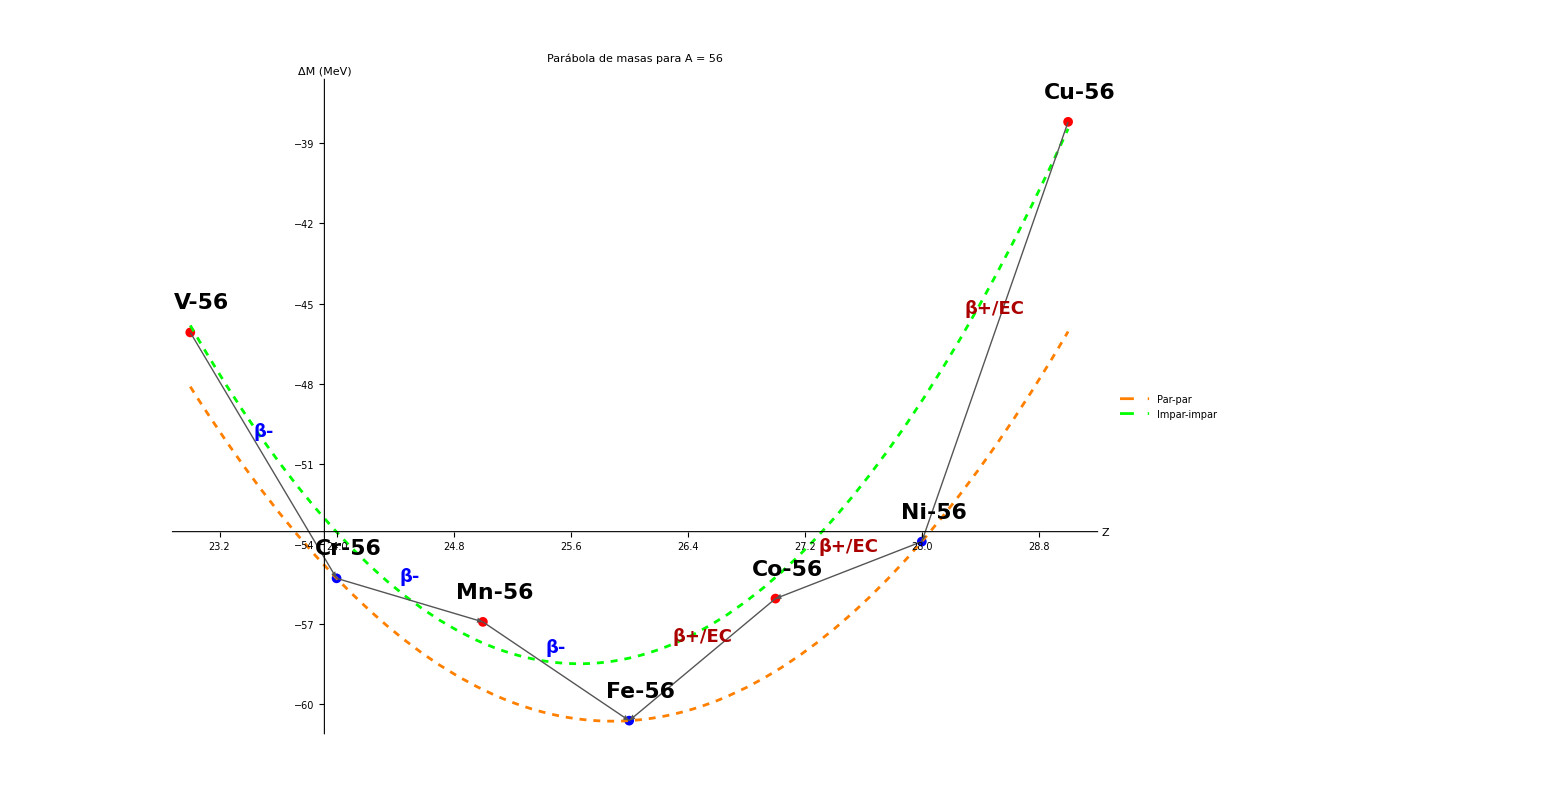

```mathematica
A0=56; (*Selección del A-par*)

(* ============================================ *)
(* 2. FILTRADO ROBUSTO: columnas útiles del txt *)
(* ============================================ *)
(* En tu fichero:
   col 1 = A
   col 3 = Z
   col 7 = exceso de masa ΔM (MeV o keV según tabla importada)
*)

datosA = Select[
   data2,
   Length[#] >= 7 &&
   NumericQ[#[[1]]] &&
   NumericQ[#[[3]]] &&
   NumericQ[#[[7]]] &&
   #[[1]] == A0 &
];

If[Length[datosA] == 0,
   Print["No hay datos válidos para A = ", A0];
   Abort[];
];

(* =================================== *)
(* 3. CONSTRUIR {Z, ΔM} Y ORDENAR      *)
(* =================================== *)
datosOrdenados = SortBy[datosA, #[[3]] &];

datosUnicos = Values @ GroupBy[
   datosOrdenados,
   #[[3]] &,
   First @ MinimalBy[#, #[[7]] &] &
];

datosUnicos = SortBy[datosUnicos, #[[3]] &];

datosM = ({#[[3]], #[[7]]} &) /@ datosUnicos;
elementos = #[[2]] & /@ datosUnicos;

(* =================================== *)
(* 4. ENCONTRAR EL MÍNIMO              *)
(* =================================== *)

minimo = MinimalBy[datosM, Last][[1]];
zMin = minimo[[1]];
mMin = minimo[[2]];
ymin = Min[subdatos[[All, 2]]];
ymax = Max[subdatos[[All, 2]]];
dy = ymax - ymin;
posMin = First@FirstPosition[datosM, minimo];

(* ================================================= *)
(* 5. TOMAR 7 PUNTOS: 3 A CADA LADO DEL MÍNIMO       *)
(* ================================================= *)

nLado = 3;

i1 = Max[1, posMin - nLado];
i2 = Min[Length[datosM], posMin + nLado];

subdatos = datosM[[i1 ;; i2]];
subelementos=elementos[[i1 ;; i2]];

(* Si no salen 7 porque el mínimo está cerca de un borde, intentamos recentrar *)
If[Length[subdatos] < 2 nLado + 1 && Length[datosM] >= 2 nLado + 1,
   If[i1 == 1,
      subdatos = datosM[[1 ;; 2 nLado + 1]],
      subdatos = datosM[[-(2 nLado) ;; -1]]
   ];
];

(* Recalcular mínimo local por seguridad *)
minimoSub = MinimalBy[subdatos, Last][[1]];
zMinSub = minimoSub[[1]];
mMinSub = minimoSub[[2]];
posMinSub = First@FirstPosition[subdatos, minimoSub];


(* ============================ *)
(* 6. SEPARAR PAR/IMPAR         *)
(* ============================ *)

pares = Select[subdatos, EvenQ[#[[1]]] &];
impares = Select[subdatos, OddQ[#[[1]]] &];

(* ============================ *)
(* 7. AJUSTE PARABÓLICO         *)
(* ============================ *)

fitpar = Fit[pares, {1, x, x^2}, x];
fitimpar=Fit[impares, {1, x, x^2}, x];

xmin = Min[subdatos[[All, 1]]];
xmax = Max[subdatos[[All, 1]]];


(* ============================ *)
(* 8. FLECHAS AUTOMÁTICAS       *)
(* ============================ *)

(* Flechas de los núcleos con Z < Zmin hacia la derecha: beta- *)
flechasIzq = Table[
   Arrow[{subdatos[[i]], subdatos[[i + 1]]}],
   {i, 1, posMinSub - 1}
];

(* Flechas de los núcleos con Z > Zmin hacia la izquierda: beta+ / EC *)
flechasDer = Table[
   Arrow[{subdatos[[i]], subdatos[[i - 1]]}],
   {i, Length[subdatos], posMinSub + 1, -1}
];

(* Etiquetas automáticas en puntos medios *)
etiquetasIzq = Table[
   Text[
     Style["β-", 18, Blue, Bold],
     Mean[{subdatos[[i]], subdatos[[i + 1]]}] + {0, 0.04 (Max[subdatos[[All, 2]]] - Min[subdatos[[All, 2]]])}
   ],
   {i, 1, posMinSub - 1}
];

etiquetasDer = Table[
   Text[
     Style["β+/EC", 18, Darker[Red], Bold],
     Mean[{subdatos[[i]], subdatos[[i - 1]]}] + {0, 0.04 (Max[subdatos[[All, 2]]] - Min[subdatos[[All, 2]]])}
   ],
   {i, Length[subdatos], posMinSub + 1, -1}
];

etiquetasElementos = Table[
   Inset[
     Style[
       Row[{ToString[subelementos[[i]]], "-", A0}],
       22, Black, Bold,
       Background -> White
     ],
     N[subdatos[[i]] + {0.08, 0.05*dy}]
   ],
   {i, Length[subdatos]}
];

(* ============================ *)
(* 9. TABLA DE DATOS USADOS     *)
(* ============================ *)

tablaDatos = TableForm[
   MapThread[
   {#1[[1]],#1[[2]],#2} &,
   {subdatos, subelementos}
   ],
   TableHeadings -> {None, {"Z", "Exceso de masa", "Elemento"}}
];

Print["Datos usados:"];
Print[tablaDatos];


(* ============================ *)
(* 10. GRÁFICA FINAL            *)
(* ============================ *)

grafica = Show[
   {
    ListPlot[
      pares,
      PlotStyle -> Blue,
      PlotMarkers -> {Automatic, 10}
    ],
    ListPlot[
      impares,
      PlotStyle -> Red,
      PlotMarkers -> {Automatic, 10}
    ],
    Plot[
      fitpar,
      {x, xmin, xmax},
      PlotStyle -> {Dashed, Orange},
      PlotLegends -> Placed[{Style["Par-par",18]}, {0.3, 0.85}]
    ],
    Plot[
    fitimpar,
    {x, xmin, xmax},
    PlotStyle->{Dashed, Green},
    PlotLegends -> Placed[{Style["Impar-impar",18]}, {0.3, 0.8}]
    ],
    Graphics[
      {
       Thick, Darker[Gray],
       flechasIzq,
       flechasDer,
       etiquetasIzq,
       etiquetasDer,
       etiquetasElementos
      }
    ]
   },
   AxesLabel -> {"Z", "ΔM (MeV)"},
   PlotLabel -> Style[Row[{"Parábola de masas para ", Style["A", Italic], " = ", A0}], 32, Bold],
   PlotRange -> All,
   ImageSize -> 1300
];

grafica
```

Datos usados:

Z | Exceso de masa | Elemento
41 | -78.886 | Nb
42 | -83.5147 | Mo
43 | -86.339 | Tc
44 | -87.9529 | Ru
45 | -87.412 | Rh
46 | -85.432 | Pd
47 | -81.334 | Ag

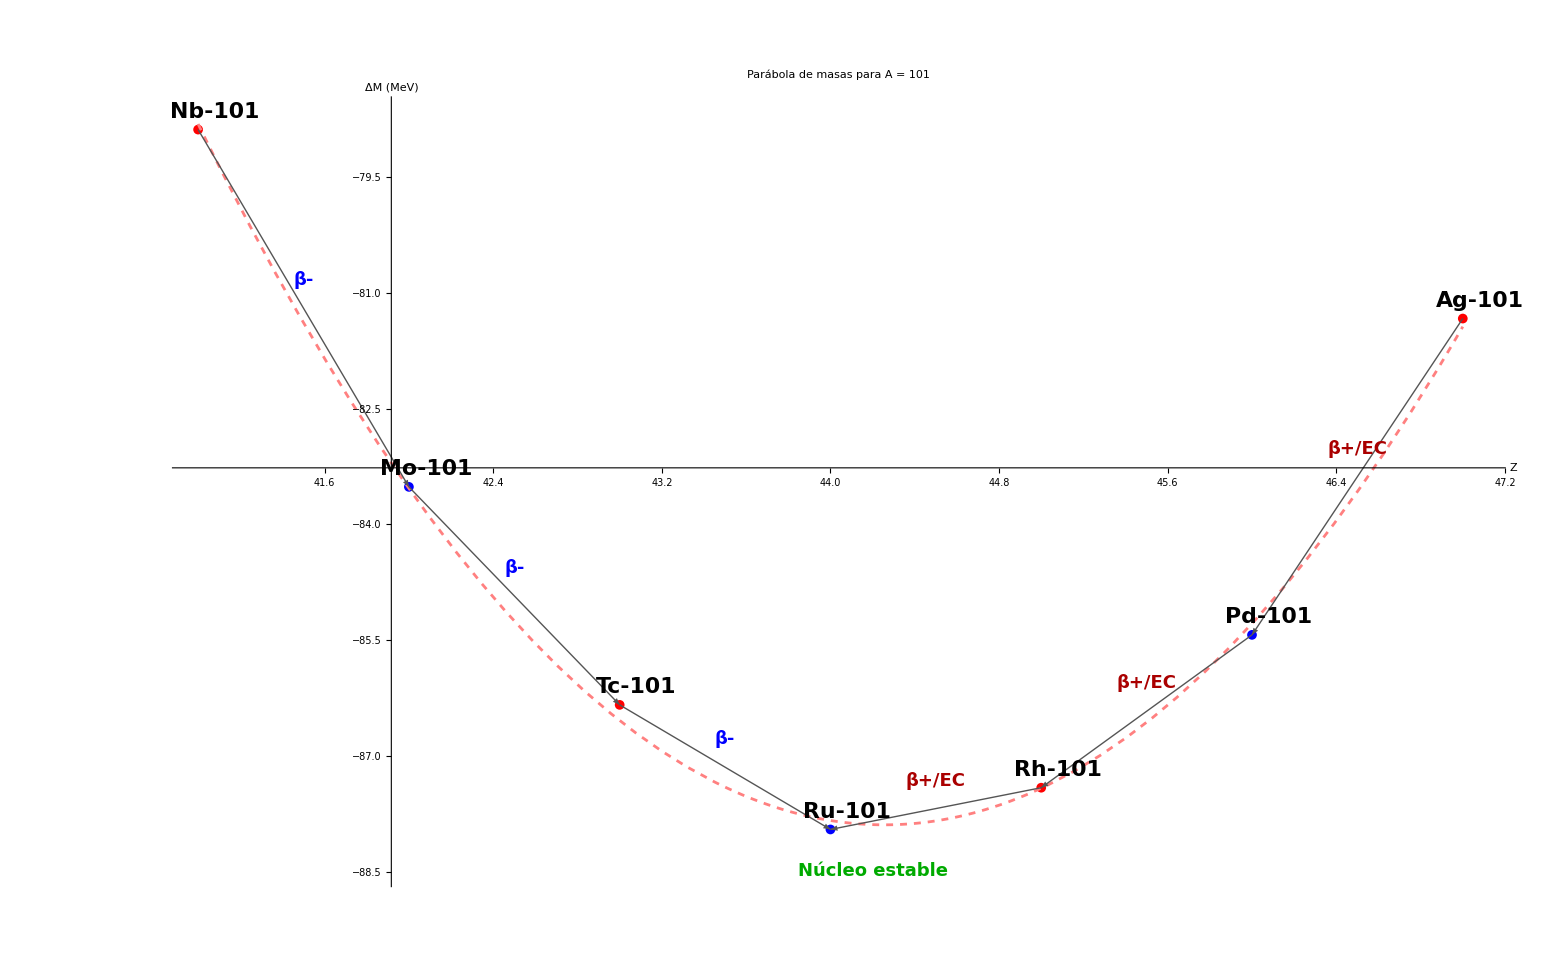

```mathematica
A0=101; (*Selección del A-par*)

(* ============================================ *)
(* 2. FILTRADO ROBUSTO: columnas útiles del txt *)
(* ============================================ *)
(* En tu fichero:
   col 1 = A
   col 3 = Z
   col 7 = exceso de masa ΔM (MeV o keV según tabla importada)
*)

datosA = Select[
   data2,
   Length[#] >= 7 &&
   NumericQ[#[[1]]] &&
   NumericQ[#[[3]]] &&
   NumericQ[#[[7]]] &&
   #[[1]] == A0 &
];

If[Length[datosA] == 0,
   Print["No hay datos válidos para A = ", A0];
   Abort[];
];

(* =================================== *)
(* 3. CONSTRUIR {Z, ΔM} Y ORDENAR      *)
(* =================================== *)
datosOrdenados = SortBy[datosA, #[[3]] &];

datosUnicos = Values @ GroupBy[
   datosOrdenados,
   #[[3]] &,
   First @ MinimalBy[#, #[[7]] &] &
];

datosUnicos = SortBy[datosUnicos, #[[3]] &];

datosM = ({#[[3]], #[[7]]} &) /@ datosUnicos;
elementos = #[[2]] & /@ datosUnicos;

(* =================================== *)
(* 4. ENCONTRAR EL MÍNIMO              *)
(* =================================== *)

minimo = MinimalBy[datosM, Last][[1]];
posMin = First@FirstPosition[datosM, minimo];

(* ================================================= *)
(* 5. TOMAR 7 PUNTOS: 3 A CADA LADO DEL MÍNIMO       *)
(* ================================================= *)

nLado = 3;

i1 = Max[1, posMin - nLado];
i2 = Min[Length[datosM], posMin + nLado];

subdatos = datosM[[i1 ;; i2]];
subelementos=elementos[[i1 ;; i2]];

ymin = Min[subdatos[[All, 2]]];
ymax = Max[subdatos[[All, 2]]];
dy = ymax - ymin;

(* Si no salen 7 porque el mínimo está cerca de un borde, intentamos recentrar *)
If[Length[subdatos] < 2 nLado + 1 && Length[datosM] >= 2 nLado + 1,
   If[i1 == 1,
      subdatos = datosM[[1 ;; 2 nLado + 1]],
      subdatos = datosM[[-(2 nLado) ;; -1]]
   ];
];

(* Recalcular mínimo local por seguridad *)
minimoSub = MinimalBy[subdatos, Last][[1]];
zMinSub = minimoSub[[1]];
mMinSub = minimoSub[[2]];
posMinSub = First@FirstPosition[subdatos, minimoSub];

(* ============================ *)
(* 7. SEPARAR PAR/IMPAR         *)
(* ============================ *)

pares = Select[subdatos, EvenQ[#[[1]]] &];
impares = Select[subdatos, OddQ[#[[1]]] &];

(* ============================ *)
(* 8. FLECHAS AUTOMÁTICAS       *)
(* ============================ *)

(* Flechas de los núcleos con Z < Zmin hacia la derecha: beta- *)
flechasIzq = Table[
   Arrow[{subdatos[[i]], subdatos[[i + 1]]}],
   {i, 1, posMinSub - 1}
];

(* Flechas de los núcleos con Z > Zmin hacia la izquierda: beta+ / EC *)
flechasDer = Table[
   Arrow[{subdatos[[i]], subdatos[[i - 1]]}],
   {i, Length[subdatos], posMinSub + 1, -1}
];

(* Etiquetas automáticas en puntos medios *)
etiquetasIzq = Table[
   Text[
     Style["β-", 18, Blue, Bold],
     Mean[{subdatos[[i]], subdatos[[i + 1]]}] + {0, 0.04 (Max[subdatos[[All, 2]]] - Min[subdatos[[All, 2]]])}
   ],
   {i, 1, posMinSub - 1}
];

etiquetasDer = Table[
   Text[
     Style["β+/EC", 18, Darker[Red], Bold],
     Mean[{subdatos[[i]], subdatos[[i - 1]]}] + {0, 0.04 (Max[subdatos[[All, 2]]] - Min[subdatos[[All, 2]]])}
   ],
   {i, Length[subdatos], posMinSub + 1, -1}
];

etiquetaEstable = {
   Text[
     Style["Núcleo estable", 18, Darker[Green], Bold],
     minimoSub + {0.2, -0.06 (Max[subdatos[[All, 2]]] - Min[subdatos[[All, 2]]])}
   ]
};

etiquetasElementos = Table[
   Inset[
     Style[
       Row[{ToString[subelementos[[i]]], "-", A0}],
       22, Black, Bold,
       Background -> White
     ],
     N[subdatos[[i]] + {0.08, 0.025*dy}]
   ],
   {i, Length[subdatos]}
];

(* ============================ *)
(* 9. TABLA DE DATOS USADOS     *)
(* ============================ *)

tablaDatos = TableForm[
   MapThread[
   {#1[[1]],#1[[2]],#2} &,
   {subdatos, subelementos}
   ],
   TableHeadings -> {None, {"Z", "Exceso de masa", "Elemento"}}
];

Print["Datos usados:"];
Print[tablaDatos];


(* ============================ *)
(* 10. GRÁFICA FINAL            *)
(* ============================ *)

grafica = Show[
   {
    ListPlot[
      pares,
      PlotStyle -> Blue,
      PlotMarkers -> {Automatic, 10}
    ],
    ListPlot[
      impares,
      PlotStyle -> Red,
      PlotMarkers -> {Automatic, 10}
    ],
    Plot[
      fit,
      {x, xmin, xmax},
      PlotStyle -> {Dashed, Pink}
    ],
    Graphics[
      {
       Thick, Darker[Gray],
       flechasIzq,
       flechasDer,
       etiquetasIzq,
       etiquetasDer,
       etiquetaEstable,
       etiquetasElementos
      }
    ]
   },
   AxesLabel -> {"Z", "ΔM (MeV)"},
   PlotLabel -> Style[Row[{"Parábola de masas para ", Style["A", Italic], " = ", A0}], 32, Bold],
   PlotRange -> All,
   ImageSize -> 1300
];

grafica
```